## Решение ДУ

### Общее решение

```mathematica
ClearAll["Global`*"]
sol=DSolve[
x y'[x]-y[x]==x^3y[x]^2,
y[x],x]
yx=y[x]/.sol[[1]]
```

{{y[x]→-(4 x)/(x^4-4 C[1])}}

-(4 x)/(x^4-4 C[1])

### Задача Коши

{{y[x]→-(4 x)/(-5+x^4)}}

-(4 x)/(-5+x^4)

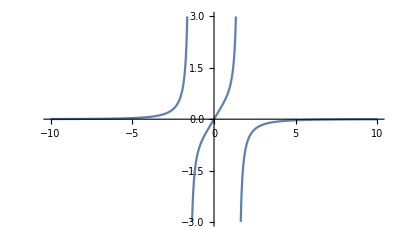

```mathematica
ClearAll["Global`*"]
x0=1;
y0=1;
sol=DSolve[{
x y'[x]-y[x]==x^3y[x]^2,
y[x0]==y0
},y[x],x]
yx=y[x]/.sol[[1]]
Plot[yx,{x,-10,10},PlotRange->{-3,3}]
```

### Поле направлений

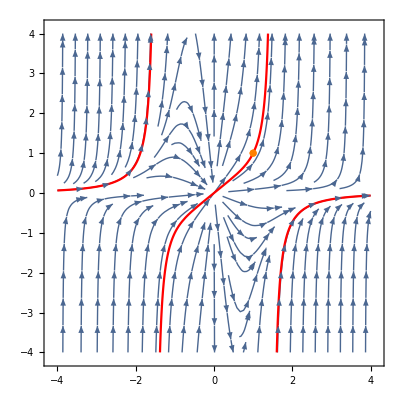

```mathematica
a=4;
Show[
StreamPlot[{1,(x^3y^2+y)/x},{x,-a,a},{y,-a,a}],
Plot[yx,{x,-a,a},PlotStyle->Red,Exclusions->{Denominator[yx]==0},PlotRange->{-a,a}],
ListPlot[{{x0,y0}},PlotStyle->Orange]
]
```

## Системы ДУ

#### ДУ не имеет решения в виде функций

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[t]→√2 √(C[1]+4 Sin[1/2 (π-4 JacobiAmplitude[1/2 (-√2 t √(4+C[1])-√(4+C[1]) C[2]),8/(4+C[1])])]),x[t]→1/2 (π-4 JacobiAmplitude[1/2 (-√2 t √(4+C[1])-√(4+C[1]) C[2]),8/(4+C[1])])},{y[t]→-√2 √(C[1]+4 Sin[1/2 (π-4 JacobiAmplitude[1/2 (√2 t √(4+C[1])-√(4+C[1]) C[2]),8/(4+C[1])])]),x[t]→1/2 (π-4 JacobiAmplitude[1/2 (√2 t √(4+C[1])-√(4+C[1]) C[2]),8/(4+C[1])])}}

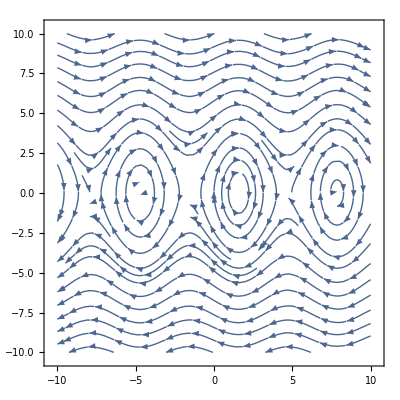

```mathematica
ClearAll["Global`*"]
a=10;
solF=DSolve[{
x'[t]==y[t],
y'[t]==4Cos[x[t]]
},{x[t],y[t]},t]
xt=x[t]/.solF[[1]];
yt=y[t]/.solF[[1]];
Show[
StreamPlot[{y,4Cos[x]},{x,-a,a},{y,-a,a}],
ParametricPlot[{xt,yt},{t,-a,a},PlotStyle->Red]
]
```

#### ДУ не имеет решения в виде функций, но имеет решение в виде интерполяционной кривой

{{x[t]→InterpolatingFunction[{{-10., 10.}}, <>][t],y[t]→InterpolatingFunction[{{-10., 10.}}, <>][t]}}

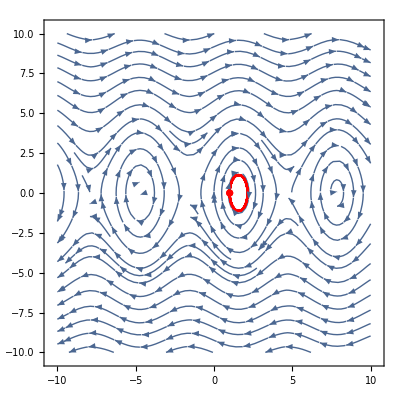

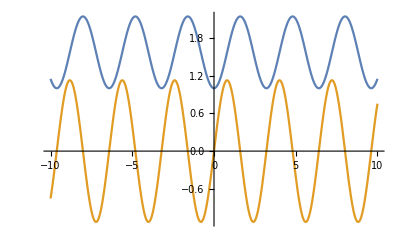

```mathematica
ClearAll["Global`*"]
a=10;
t0=0;
x0=1;
y0=0;
sol=NDSolve[{
x'[t]==y[t],
y'[t]==4Cos[x[t]],
x[t0]==x0,
y[t0]==y0
},{x[t],y[t]},
{t,-a,a}]
xt=x[t]/.sol[[1]];
yt=y[t]/.sol[[1]];

Show[
StreamPlot[{y,4Cos[x]},{x,-a,a},{y,-a,a}],
ParametricPlot[{xt,yt},{t,-a,a},PlotStyle->Red],
ListPlot[{{x0,y0}},PlotStyle->Red]
]

Plot[{xt,yt},{t,-a,a}]
```